## Hopf Fussmann - Figure with power spectra and bifurcation diagram

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import data

### Raw data files

```mathematica
(* power spectrum data *)
pspecChlorRaw=Import["data_export/pspec_chlor.csv"];
pspecBrachRaw=Import["data_export/pspec_brach.csv"];
(* time-series data *)
seriesRaw=Import["data_export/series_data.csv"];
(* ews data *)
ewsChlorRaw=Import["data_export/ews_chlor.csv"];
ewsBrachRaw=Import["data_export/ews_brach.csv"];
```

### Put Data into array form

```mathematica
deltaVals=Union[seriesRaw[[2;;,1]]]
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.89,0.95,1.,1.15,1.17,1.24,1.37}

```mathematica
(* delta values for plot *)
deltaValsFilt={0.04,0.32,0.64,0.95,1.17,1.37};
```

```mathematica
(* time-series data *)
seriesRaw[[1]]
```

{Delta,Time,Chlorella,Brachionus}

```mathematica
(* chlorella time-series *)
seriesChlor=Table[
Cases[seriesRaw,
{deltaValsFilt[[i]],_,_,_}][[;;,{2,3}]],
{i,1,Length[deltaValsFilt]}];

seriesBrach=Table[
Cases[seriesRaw,
{deltaValsFilt[[i]],_,_,_}][[;;,{2,4}]],
{i,1,Length[deltaValsFilt]}];
```

```mathematica
(* power spectrum data *)
pspecChlorRaw[[1]]
```

{Delta,Frequency,Empirical}

```mathematica
pspecChlor=Table[
Cases[pspecChlorRaw,
{deltaValsFilt[[i]],_,_}][[;;,{2,3}]],
{i,1,Length[deltaValsFilt]}];
```

```mathematica
pspecBrach=Table[
Cases[pspecBrachRaw,
{deltaValsFilt[[i]],_,_}][[;;,{2,3}]],
{i,1,Length[deltaValsFilt]}];
```

```mathematica
(* ews data *)
ewsChlorRaw[[1]]
```

{Delta,Variance,Coefficient of variation,Lag-1 AC,Lag-2 AC,Lag-10 AC,Smax,AIC fold,AIC hopf,AIC null}

```mathematica
(* index positions of chosen delta values *)
indexDelta=Position[ewsChlorRaw[[;;,1]],#]&/@deltaValsFilt//Flatten;
```

```mathematica
(* index positions of AIC metrics *)
indexAIC=Position[ewsChlorRaw[[1]],#]&/@{"AIC fold","AIC hopf","AIC null"}//Flatten;
```

```mathematica
(* index position of Smax *)
indexSmax = Position[ewsChlorRaw[[1]],"Smax"]//Flatten;
```

```mathematica
ewsChlorRaw[[1]]
```

{Delta,Variance,Coefficient of variation,Lag-1 AC,Lag-2 AC,Lag-10 AC,Smax,AIC fold,AIC hopf,AIC null}

```mathematica
aicChlor=ewsChlorRaw[[indexDelta,indexAIC]];
smaxChlor=ewsChlorRaw[[indexDelta,indexSmax]]//Flatten;

aicBrach=ewsBrachRaw[[indexDelta,indexAIC]];
smaxBrach=ewsBrachRaw[[indexDelta,indexSmax]]//Flatten;
```

## Time-series figures

```mathematica
(* figure parameters *)
aRatio=0.9;
imgSize=220;
labelPos={0.5,1.15};
padding={{50,50},{50,30}};
```

### Figure 1

```mathematica
(* figure number *)
fig=1;
```

```mathematica
series=seriesChlor[[fig]];
fig1Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Automatic,None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]],
Text[Style["b",14,Bold],Scaled[{0.1,0.5}]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig1Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{None,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

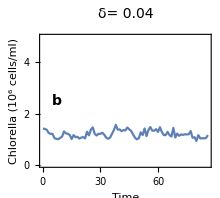
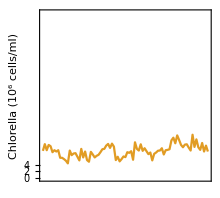

```mathematica
(* overlay the plots *)
fig1=Overlay[{fig1Chlorella,fig1Brach}]
```

### Figure 2

```mathematica
(* figure number *)
fig=2;
```

```mathematica
series=seriesChlor[[fig]];
fig2Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig2Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

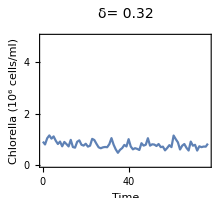
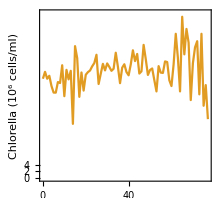

```mathematica
(* overlay the plots *)
fig2=Overlay[{fig2Chlor,fig2Brach}]
```

### Figure 3

```mathematica
(* figure number *)
fig=3;
```

```mathematica
series=seriesChlor[[fig]];
fig3Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig3Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

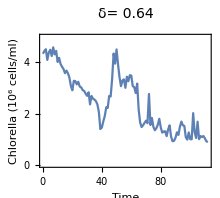
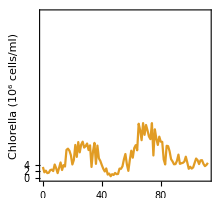

```mathematica
(* overlay the plots *)
fig3=Overlay[{fig3Chlor,fig3Brach}]
```

### Figure 4

```mathematica
(* figure number *)
fig=4;
```

```mathematica
series=seriesChlor[[fig]];
fig4Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig4Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

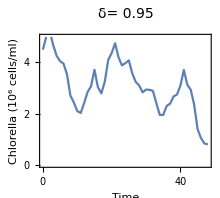
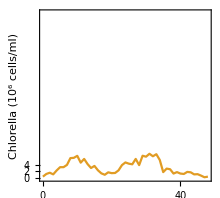

```mathematica
(* overlay the plots *)
fig4=Overlay[{fig4Chlor,fig4Brach}]
```

### Figure 5

```mathematica
(* figure number *)
fig=5;
```

```mathematica
series=seriesChlor[[fig]];
fig5Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig5Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

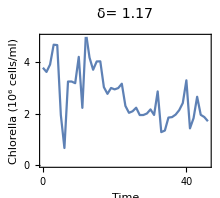
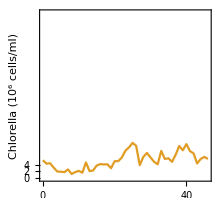

```mathematica
(* overlay the plots *)
fig5=Overlay[{fig5Chlor,fig5Brach}]
```

### Figure 6

```mathematica
(* figure number *)
fig=6;
```

```mathematica
series=seriesChlor[[fig]];
fig6Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaValsFilt[[fig]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[fig]];
fig6Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

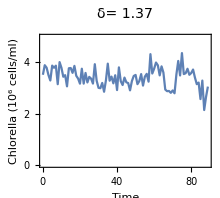
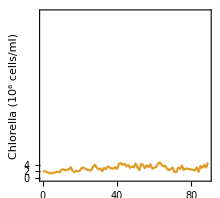

```mathematica
(* overlay the plots *)
fig6=Overlay[{fig6Chlor,fig6Brach}]
```

## Power spectrum figures

We normalise the power spectrum plots so they are on the same scale for the figure - saves using many y axes - we are just showing qualitative features of spectrum, quantiitative feature given by Smax.

```mathematica
(* figure parameters *)
wmax=2.7; (* x-axes limit *)
wTicks=Range[-2,2];
(* y axis plot range *)
yRangeChlor={0,2};
yRangeBrach={0,2};

(* figure params *)
imgpaddingPsd={{50,50},{40,20}};
imgSizePsd=220;
plotNormMax=2;
```

### Figure 1 PSD

```mathematica
(* figure number *)
fig=1;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

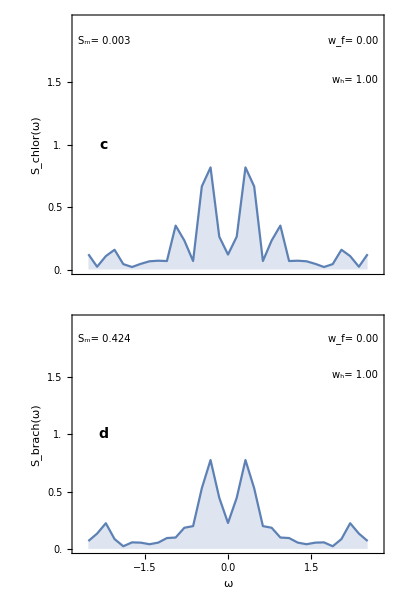

```mathematica
(* make plot for grid *)
figPsd1Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Range[0,1.8,0.5],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["c",14,Bold],Scaled[{0.1,0.5}]]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{Automatic,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["d",14,Bold],Scaled[{0.1,0.5}]]}
]}}
,Spacings->{-2,-3}]
```

### Figure 2 PSD

```mathematica
(* figure number *)
fig=2;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

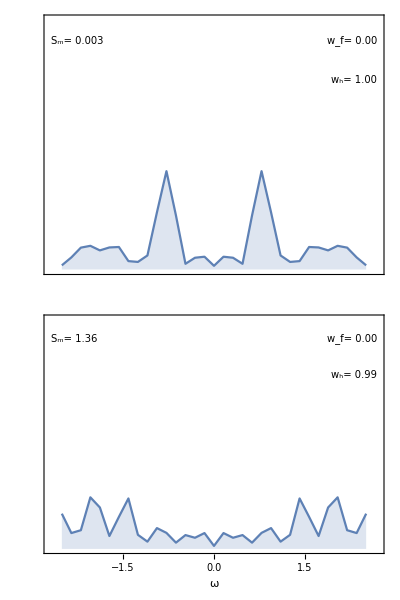

```mathematica
(* make plot for grid *)
figPsd2Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 3 PSD

```mathematica
(* figure number *)
fig=3;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

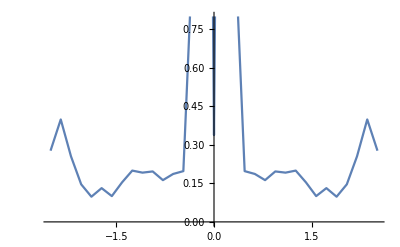

```mathematica
ListLinePlot[psDataBrach]
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

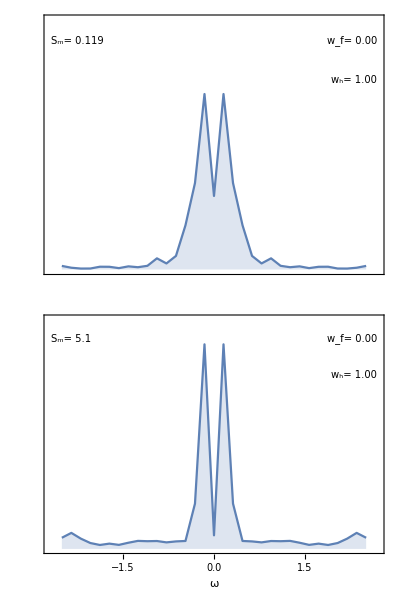

```mathematica
(* make plot for grid *)
figPsd3Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 4 PSD

```mathematica
(* figure number *)
fig=4;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

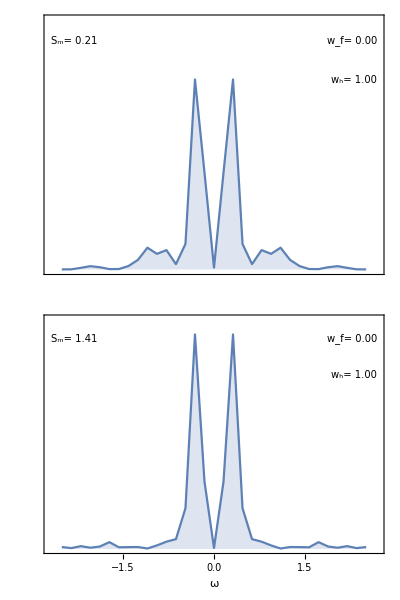

```mathematica
(* make plot for grid *)
figPsd4Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 5 PSD

```mathematica
(* figure number *)
fig=5;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

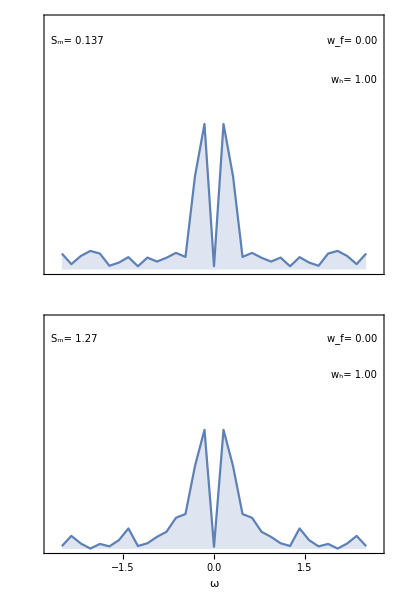

```mathematica
(* make plot for grid *)
figPsd5Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 6 PSD

```mathematica
(* figure number *)
fig=6;
```

```mathematica
(* power spectrum data *)
psDataChlor=pspecChlor[[fig]];
psDataBrach=pspecBrach[[fig]];
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

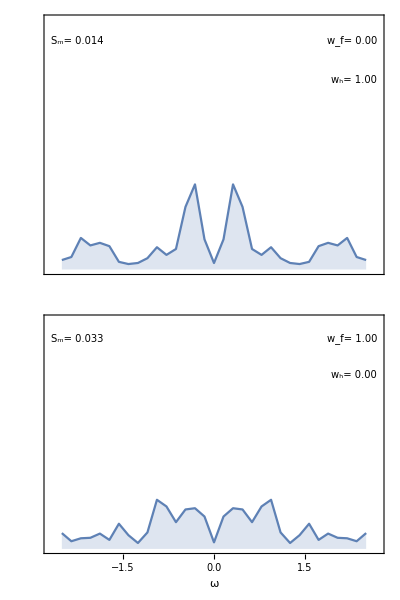

```mathematica
(* make plot for grid *)
figPsd6Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Automatic,None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[fig,2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[fig]],{3,3}]],10],Scaled[{0.02,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

```mathematica
smaxBrach[[fig]]
```

0.0328329

```mathematica
smaxBrach
```

{0.4242,1.36239,5.099,1.41351,1.27189,0.0328329}

```mathematica
ToString[AccountingForm[smaxBrach[[fig]],{3,3}]]
```

0.033

## Bifurcation diagram

### Import Bifurcation Data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=0.32;
expBif1b=0.64;
expBif2=1.16;
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* figure params *)
colChlor=TMBcolours[[1]];
colBrach=TMBcolours[[2]];
lt=0.004;
ltExt=0.0012;
imgs=900;
aRatio=0.22;
padding={{50,50},{30,50}};
```

### Bif Figure Code

```mathematica
(* chlorella bif *)
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"","Dilution rate δ (per day)"}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Range[0,2,0.2]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{EdgeForm[Directive[Black,Thickness[0]]],Opacity[0.05],Directive[Black],Rectangle[{expBif1a,0},{expBif1b,4200000}],
Rectangle[{expBif2-0.01,0},{expBif2+0.01,4200000}],
Opacity[1],
Directive[{Black,Thickness[1.5*ltExt]}],Line[Table[{Scaled[{0,-0.05},{deltaValsFilt[[i]],0}],
Scaled[{0,0.05},{deltaValsFilt[[i]],0}]},{i,1,Length[deltaValsFilt]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.02,0.5}]]}];
```

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotRangeClipping->False,
ImagePadding->padding];
```

### Bif Output

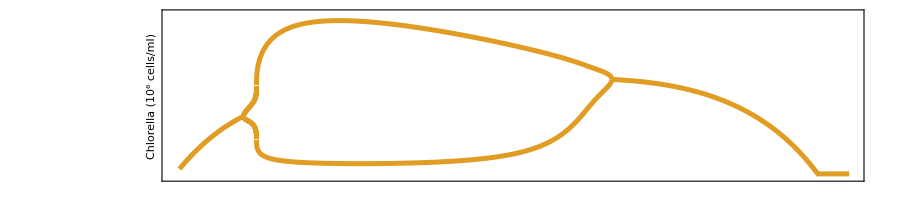
-Graphics--Graphics-

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Bring it all together

```mathematica
gridFussmann=Grid[{{bifPlot,SpanFromLeft},{fig1,fig2,fig3,fig4,fig5,fig6},{figPsd1Norm,figPsd2Norm,figPsd3Norm,figPsd4Norm,figPsd5Norm,figPsd6Norm}},Spacings->{-6.5,0}]
```

-Graphics--Graphics- |  |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

The fact that the bifurcation diagram doesn’t line up with the real data just goes to confirm that we cannot predict bifurcations from models alone - require help from generic early warning signals.

```mathematica
Export["figures/fussmann_ews_pspecs.png",gridFussmann,ImageResolution->200];
```